LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0720323,6.10282,3.61377×10^8,4.26538×10^6},{-0.0834205,11.8416,-1.92519×10^8,3.41221×10^6},{0.0217132,13.9193,2.87843×10^12,4.49015×10^9},{-0.0251461,27.0084,-1.53345×10^12,3.59202×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{528.111,462.051,437.497,427.209,422.057,419.137,417.331,416.14,415.313,414.717}

```mathematica
ListOrthoNoFric25 =  EIofN/@Range[20]
```

```mathematica
ListTransvNoFric25 =  EIofN/@Range[20]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.169466,6.94986,1.53605×10^8,3.74552×10^6},{-0.169554,18.5324,-6.28568×10^7,3.63016×10^6},{0.0754494,16.8188,8.2837×10^11,3.71607×10^9},{-0.0754887,44.8488,-3.38978×10^11,3.60163×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{540.086,464.284,438.478,427.943,422.732,419.8,417.994,416.806,415.984,415.392,414.952,414.616,414.353,414.145,413.976,413.838,413.723,413.627,413.546,413.476}

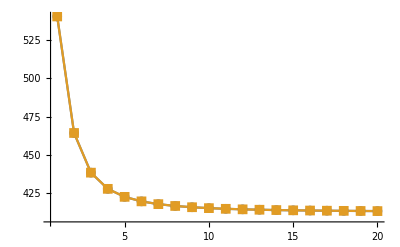

```mathematica
ListLinePlot[{ListOrthoNoFric25,ListTransvNoFric25},PlotMarkers->{Automatic, 10},PlotRange->All]
```

```mathematica
S1=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
S2={{0.000105,-6.320000000000001*^-6,-8.42*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-8.42*^-6,0,0,0},{-8.42*^-6,-8.42*^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264000000000002}};
S3={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};
```

```mathematica
S1//MatrixForm
```

(0.000105 | -6.32×10^-6 | -8.42×10^-6 | 0. | 0. | 0.
-6.32×10^-6 | 0.000118 | -9.41×10^-6 | 0. | 0. | 0.
-8.42×10^-6 | -9.41×10^-6 | 0.00002 | 0. | 0. | 0.
0. | 0. | 0. | 0.0004 | 0. | 0.
0. | 0. | 0. | 0. | 0.0005 | 0.
0. | 0. | 0. | 0. | 0. | 0.00025)

```mathematica
Mean[{S1[[1,1]],S1[[2,2]]}]
Mean[{S1[[3,1]],S1[[3,2]]}]
```

0.0001115

-8.915×10^-6

```mathematica
Ep =1/0.0001115;
vp = -6.320000000000001*^-6*(-Ep);
μp = Ep/(2*(1+vp));
1/μp
```

0.00023564

```mathematica
1/7.89746
```

0.126623

```mathematica
S={{0.0001115,-6.320000000000001*^-6,-8.915000000000002*^-6,0.0,0.0,0.0}
,{-6.320000000000001*^-6,0.0001115,-8.915000000000002*^-6,0.0,0.0,0.0}
,{-8.915000000000002*^-6,-8.915000000000002*^-6,0.00002,0.0,0.0,0.0}
,{0.0,0.0,0.0,0.00045,0.0,0.0}
,{0.0,0.0,0.0,0.0,0.00045,0.0}
,{0.0,0.0,0.0,0.0,0.0,0.00023564000000000004}};
```

```mathematica
S//MatrixForm
```

(0.0001115 | -6.32×10^-6 | -8.915×10^-6 | 0. | 0. | 0.
-6.32×10^-6 | 0.0001115 | -8.915×10^-6 | 0. | 0. | 0.
-8.915×10^-6 | -8.915×10^-6 | 0.00002 | 0. | 0. | 0.
0. | 0. | 0. | 0.00045 | 0. | 0.
0. | 0. | 0. | 0. | 0.00045 | 0.
0. | 0. | 0. | 0. | 0. | 0.00023564)

```mathematica
S3//MatrixForm
```

(0.000105 | -6.32×10^-6 | -6.32×10^-6 | 0 | 0 | 0
-6.32×10^-6 | 0.000105 | -6.32×10^-6 | 0 | 0 | 0
-6.32×10^-6 | -6.32×10^-6 | 0.000105 | 0 | 0 | 0
0 | 0 | 0 | 0.0004 | 0 | 0
0 | 0 | 0 | 0 | 0.0004 | 0
0 | 0 | 0 | 0 | 0 | 0.0004)

```mathematica
2*0.0004/(0.000105+6.320000000000001*^-6)
```

7.18649

```mathematica
Limit[P[2,x],x->1,Direction->"FromBelow"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

0.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.07332,32.6182,2.42527×10^7,798047.},{-0.0690582,1056.69,-104095.,5.58917×10^6},{1.1085,159.727,5.63826×10^10,3.91293×10^8},{-0.0713219,5174.47,-2.41999×10^8,2.74044×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{{1387.35,1335.81},{1132.54,1003.08},{881.471,722.145},{679.782,533.011},{528.111,412.128},{417.368,334.745},{338.565,284.725},{284.499,252.478},{249.576,232.361},{229.379,220.995},{220.304,216.285},{219.319,216.823},{223.805,221.478},{231.452,229.078},{240.176,238.161},{248.103,246.89},{253.625,253.25},{255.606,255.587},{253.625,253.25},{248.103,246.89},{240.176,238.161},{231.452,229.078},{223.805,221.478},{219.319,216.823},{220.304,216.285},{229.379,220.995},{249.576,232.361},{284.499,252.478},{338.565,284.725},{417.368,334.745},{528.111,412.128},{679.782,533.011},{881.471,722.145},{1132.54,1003.08},{1387.35,1335.81},{1387.35,1335.81},{1132.54,1003.08},{881.471,722.145},{679.782,533.011},{528.111,412.128},{417.368,334.745},{338.565,284.725},{284.499,252.478},{249.576,232.361},{229.379,220.995},{220.304,216.285},{219.319,216.823},{223.805,221.478},{231.452,229.078},{240.176,238.161},{248.103,246.89},{253.625,253.25},{255.606,255.587},{253.625,253.25},{248.103,246.89},{240.176,238.161},{231.452,229.078},{223.805,221.478},{219.319,216.823},{220.304,216.285},{229.379,220.995},{249.576,232.361},{284.499,252.478},{338.565,284.725},{417.368,334.745},{528.111,412.128},{679.782,533.011},{881.471,722.145},{1132.54,1003.08},{1387.35,1335.81}}

## Single layer EI as a function of angle ϕ, Orthotropic

```mathematica
EIofAngle[ψ_]:=Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ];
r0=2*10^-3;
rN=14*10^-3;
Νl=1;
φ0=ψ;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[Νl];
nφ[n_]:=φ0;
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
(*S={{0.000105,-6.320000000000001*^-6,-8.42*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-8.42*^-6,0,0,0},{-8.42*^-6,-8.42*^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264000000000002}};*)
(*S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};*)φφ
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
(*{φ1,φ2} = {π,π}*)
(*nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;*)
Κ[i_,n_]:=ΚMat[n][[i]];
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
EIlimit=-(rN^4-r0^4)/4(Sum[α[i,1]*P[i,1](m[i,1]+2),{i,4}]+4γ[1]);
{EI[Νl],EIlimit}
]
ψList = Join[Range[-π+5.π/180,-5.π/180,5.π/180],Range[5.π/180,π-5.π/180,5.π/180]];
ListEIofAngle=EIofAngle/@ψList
```

```mathematica
Line
```

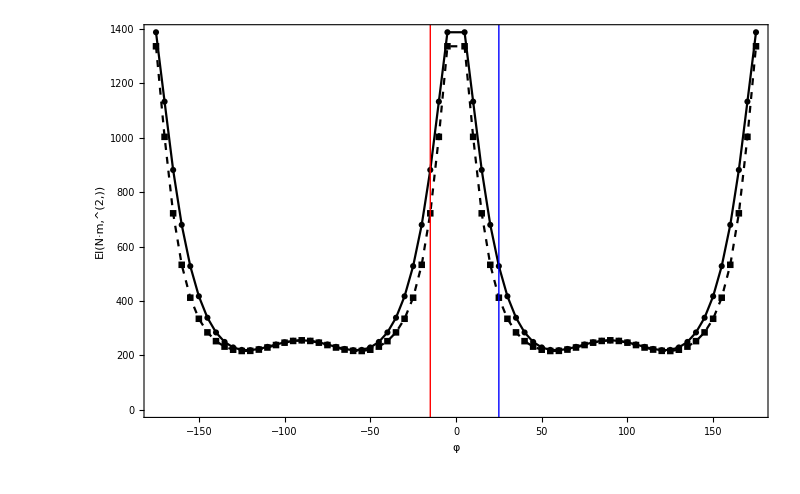

```mathematica
p1 =ListPlot[{Transpose[{ψList/π*180,ListEIofAngle[[;;,1]]}],Transpose[{ψList/π*180,ListEIofAngle[[;;,2]]}]},Joined->True,PlotRange->All,PlotStyle->{Directive[Black],Directive[Black,Dashed]},PlotMarkers->Automatic,
ImageSize->800,GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24],Frame->True,BaseStyle->{Black,FontFamily->"Times",24}
,FrameStyle->Directive[FontFamily->"Times",Black,20],FrameLabel->{Style["φ",Black,FontFamily->"Times",24],Style["EI(N·m,^(2,))",Black,FontFamily->"Times",24]}];
Show[p1,Graphics[{Red,Line[{{-15,-100},{-15,1500}}]}]
,Graphics[{Blue,Line[{{25,-100},{25,1500}}]}]]
```

## Single layer EI as a function of angle ϕ, Transversely Orthotropic

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.992804,53.0814,2.62195×10^7,490394.},{-0.0330783,4010.14,260775.,5.04424×10^6},{0.989541,324.539,6.31606×10^10,1.92581×10^8},{-0.0329695,24517.9,6.28185×10^8,1.9809×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{{1376.06,1313.47},{1108.05,955.86},{853.384,671.382},{652.277,488.324},{501.888,374.87},{392.445,303.87},{315.138,258.929},{263.029,230.741},{230.689,214.021},{213.746,205.732},{208.547,204.093},{211.947,207.994},{221.168,216.556},{233.685,228.733},{247.111,242.902},{259.116,256.601},{267.488,266.728},{270.502,270.487},{267.488,266.728},{259.116,256.601},{247.111,242.902},{233.685,228.733},{221.168,216.556},{211.947,207.994},{208.547,204.093},{213.746,205.732},{230.689,214.021},{263.029,230.741},{315.138,258.929},{392.445,303.87},{501.888,374.87},{652.277,488.324},{853.384,671.382},{1108.05,955.86},{1376.06,1313.47},{1376.06,1313.47},{1108.05,955.86},{853.384,671.382},{652.277,488.324},{501.888,374.87},{392.445,303.87},{315.138,258.929},{263.029,230.741},{230.689,214.021},{213.746,205.732},{208.547,204.093},{211.947,207.994},{221.168,216.556},{233.685,228.733},{247.111,242.902},{259.116,256.601},{267.488,266.728},{270.502,270.487},{267.488,266.728},{259.116,256.601},{247.111,242.902},{233.685,228.733},{221.168,216.556},{211.947,207.994},{208.547,204.093},{213.746,205.732},{230.689,214.021},{263.029,230.741},{315.138,258.929},{392.445,303.87},{501.888,374.87},{652.277,488.324},{853.384,671.382},{1108.05,955.86},{1376.06,1313.47}}

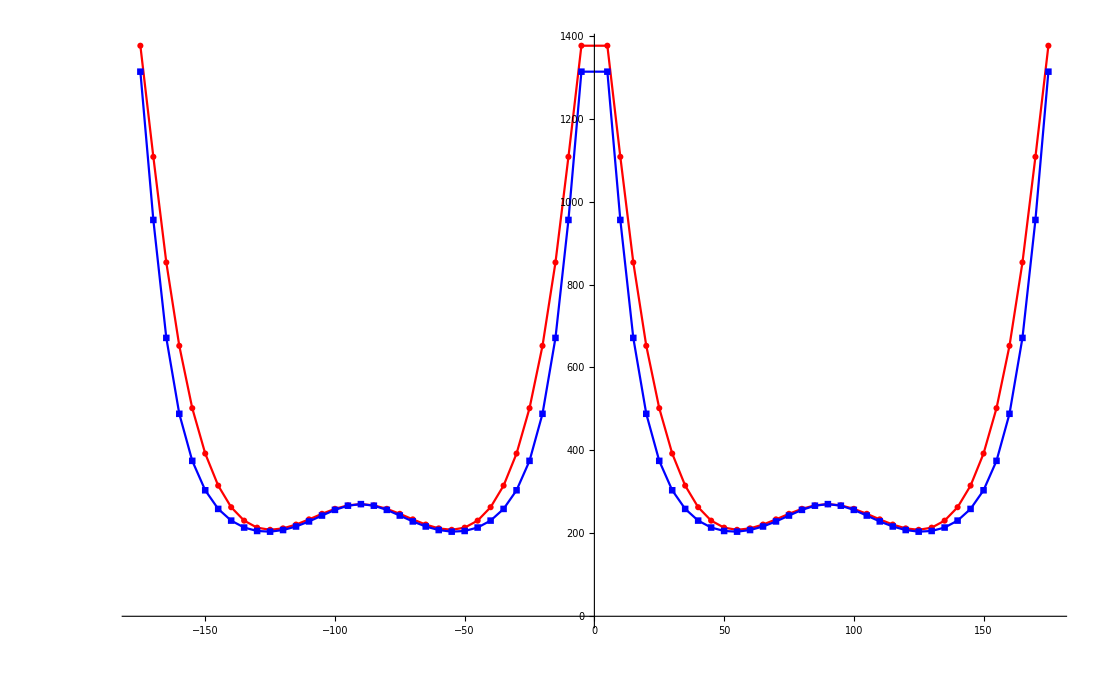

```mathematica
EIofAngle[ψ_]:=Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ];
r0=2*10^-3;
rN=14*10^-3;
Νl=1;
φ0=ψ;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[Νl];
nφ[n_]:=φ0;
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
S= S={{0.0001115,-6.320000000000001*^-6,-8.915000000000002*^-6,0.0,0.0,0.0}
,{-6.320000000000001*^-6,0.0001115,-8.915000000000002*^-6,0.0,0.0,0.0}
,{-8.915000000000002*^-6,-8.915000000000002*^-6,0.00002,0.0,0.0,0.0}
,{0.0,0.0,0.0,0.00045,0.0,0.0}
,{0.0,0.0,0.0,0.0,0.00045,0.0}
,{0.0,0.0,0.0,0.0,0.0,0.00023564000000000004}};
(*S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};*)
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
(*{φ1,φ2} = {π,π}*)
(*nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;*)
Κ[i_,n_]:=ΚMat[n][[i]];
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
EIlimit=-(rN^4-r0^4)/4(Sum[α[i,1]*P[i,1](m[i,1]+2),{i,4}]+4γ[1]);
{EI[Νl],EIlimit}
]
ψList = Join[Range[-π+5.π/180,-5.π/180,5.π/180],Range[5.π/180,π-5.π/180,5.π/180]];
ListEIofAngle=EIofAngle/@ψList
p2 =ListPlot[{Transpose[{ψList/π*180,ListEIofAngle[[;;,1]]}],Transpose[{ψList/π*180,ListEIofAngle[[;;,2]]}]},Joined->True,PlotRange->All,PlotStyle->{Red,Blue},PlotMarkers->Automatic]
```

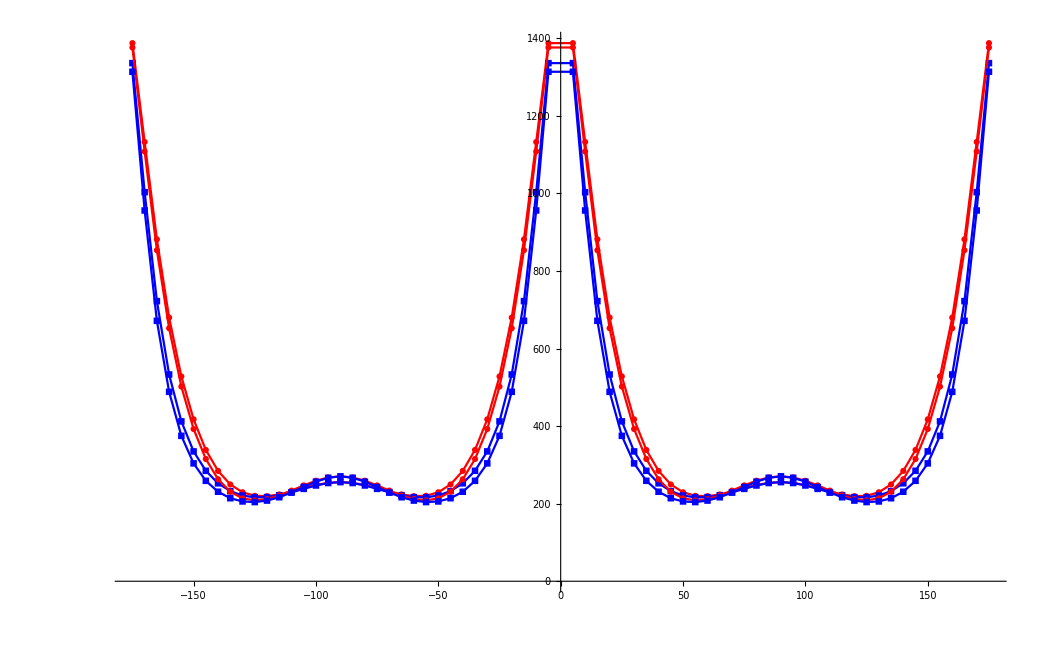

```mathematica
Show[p1,p2]
```

## Single layer EI as a function of angle ϕ, Cubic Orthotropic

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.196486,68.605,1.32482×10^8,379430.},{0.0119651,-32136.3,3.5149×10^6,-6.7145×10^6},{0.0935822,471.486,6.67862×10^11,1.3256×10^8},{0.00569872,-220856.,1.77192×10^10,-2.34581×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{{284.227,283.62},{275.798,273.711},{263.459,259.804},{249.137,244.561},{234.723,230.189},{221.829,218.142},{211.717,209.217},{205.29,203.775},{203.087,201.951},{205.29,203.775},{211.717,209.217},{221.829,218.142},{234.723,230.189},{249.137,244.561},{263.459,259.804},{275.798,273.711},{284.227,283.62},{287.231,287.231},{284.227,283.62},{275.798,273.711},{263.459,259.804},{249.137,244.561},{234.723,230.189},{221.829,218.142},{211.717,209.217},{205.29,203.775},{203.087,201.951},{205.29,203.775},{211.717,209.217},{221.829,218.142},{234.723,230.189},{249.137,244.561},{263.459,259.804},{275.798,273.711},{284.227,283.62},{284.227,283.62},{275.798,273.711},{263.459,259.804},{249.137,244.561},{234.723,230.189},{221.829,218.142},{211.717,209.217},{205.29,203.775},{203.087,201.951},{205.29,203.775},{211.717,209.217},{221.829,218.142},{234.723,230.189},{249.137,244.561},{263.459,259.804},{275.798,273.711},{284.227,283.62},{287.231,287.231},{284.227,283.62},{275.798,273.711},{263.459,259.804},{249.137,244.561},{234.723,230.189},{221.829,218.142},{211.717,209.217},{205.29,203.775},{203.087,201.951},{205.29,203.775},{211.717,209.217},{221.829,218.142},{234.723,230.189},{249.137,244.561},{263.459,259.804},{275.798,273.711},{284.227,283.62}}

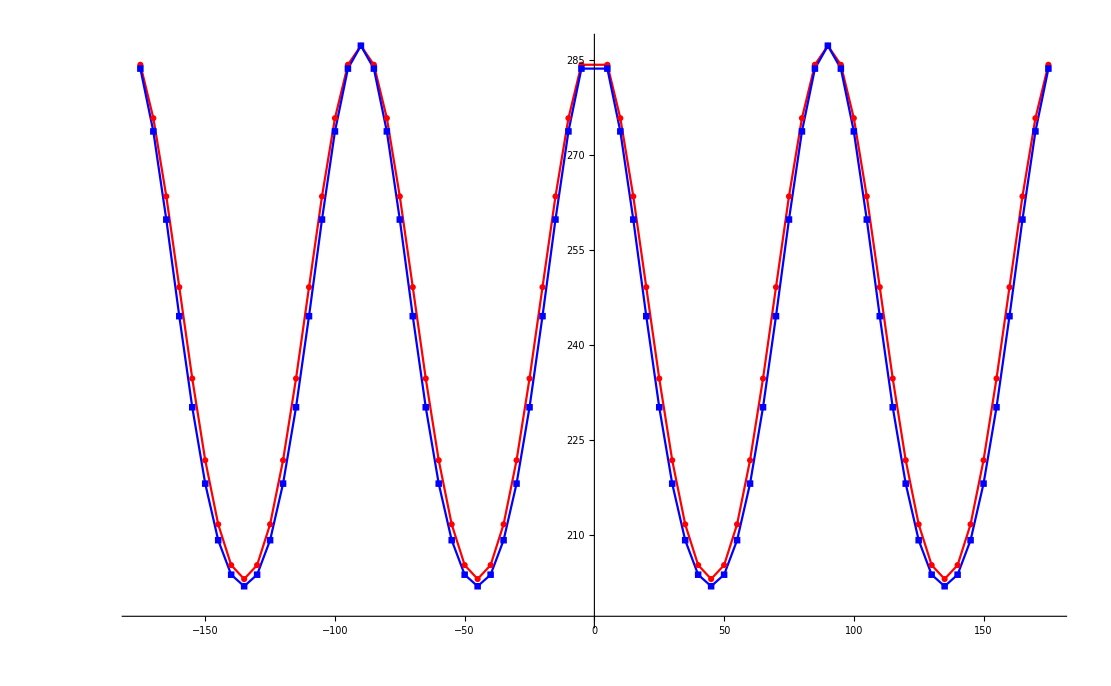

```mathematica
EIofAngle[ψ_]:=Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ];
r0=2*10^-3;
rN=14*10^-3;
Νl=1;
φ0=ψ;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[Νl];
nφ[n_]:=φ0;
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
S= S={{0.0001115,-6.320000000000001*^-6,-8.915000000000002*^-6,0.0,0.0,0.0}
,{-6.320000000000001*^-6,0.0001115,-8.915000000000002*^-6,0.0,0.0,0.0}
,{-8.915000000000002*^-6,-8.915000000000002*^-6,0.00002,0.0,0.0,0.0}
,{0.0,0.0,0.0,0.00045,0.0,0.0}
,{0.0,0.0,0.0,0.0,0.00045,0.0}
,{0.0,0.0,0.0,0.0,0.0,0.00023564000000000004}};
S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
(*{φ1,φ2} = {π,π}*)
(*nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;*)
Κ[i_,n_]:=ΚMat[n][[i]];
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
EIlimit=-(rN^4-r0^4)/4(Sum[α[i,1]*P[i,1](m[i,1]+2),{i,4}]+4γ[1]);
{EI[Νl],EIlimit}
]
ψList = Join[Range[-π+5.π/180,-5.π/180,5.π/180],Range[5.π/180,π-5.π/180,5.π/180]];
ListEIofAngle=EIofAngle/@ψList
p3 =ListPlot[{Transpose[{ψList/π*180,ListEIofAngle[[;;,1]]}],Transpose[{ψList/π*180,ListEIofAngle[[;;,2]]}]},Joined->True,PlotRange->All,PlotStyle->{Red,Blue},PlotMarkers->Automatic]
```

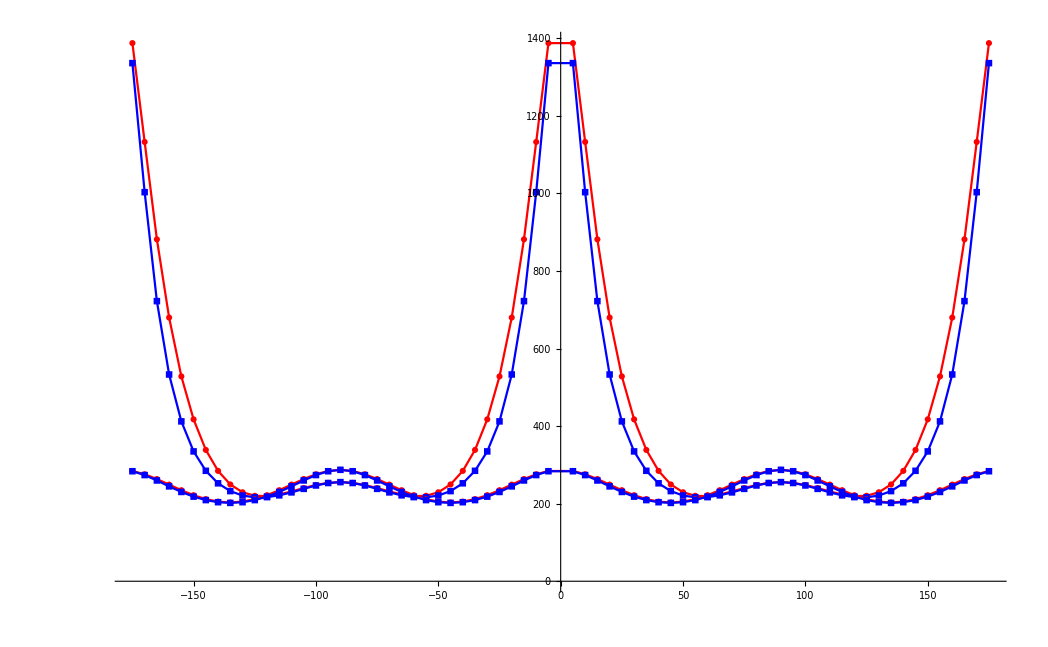

```mathematica
Show[p1,p3]
```